# Методи на Рунге-Кута за решаване задача на Коши с начално условие

## Задача 3 a) от файла

y’ = y/x+1, x ∈ [1,2]
y(1) = 0

### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.3 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.275 k1 = 0.305 k2 = 0.346667 y_точно = 0.278929 истинска грешка = 0.00392944

i = 2 x_i = 1.5 y_i = 0.600833 k1 = 0.350139 k2 = 0.385853 y_точно = 0.608198 истинска грешка = 0.00736433

i = 3 x_i = 1.75 y_i = 0.968829 k1 = 0.388404 k2 = 0.419654 y_точно = 0.979328 истинска грешка = 0.0104983

i = 4 x_i = 2. y_i = 1.37286 k1 = 0.421607 k2 = 0.449385 y_точно = 1.38629 истинска грешка = 0.0134358

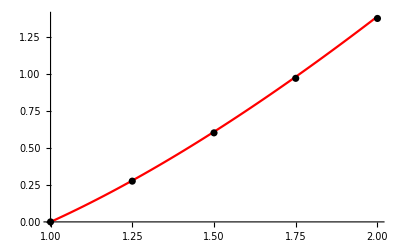

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+h,y+k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (1/2,1/2) - модифициран метод на Ойлер

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.277778 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.277778 k1 = 0.305556 k2 = 0.328283 y_точно = 0.278929 истинска грешка = 0.00115166

i = 2 x_i = 1.5 y_i = 0.606061 k1 = 0.35101 k2 = 0.370241 y_точно = 0.608198 истинска грешка = 0.00213706

i = 3 x_i = 1.75 y_i = 0.976301 k1 = 0.389472 k2 = 0.406138 y_точно = 0.979328 истинска грешка = 0.00302615

i = 4 x_i = 2. y_i = 1.38244 k1 = 0.422805 k2 = 0.437511 y_точно = 1.38629 истинска грешка = 0.00385458

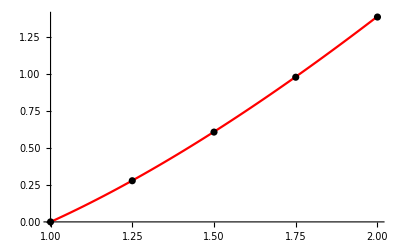

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+h/2,y+k1/2];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.285714 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.276786 k1 = 0.305357 k2 = 0.334769 y_точно = 0.278929 истинска грешка = 0.00214372

i = 2 x_i = 1.5 y_i = 0.604202 k1 = 0.3507 k2 = 0.3757 y_точно = 0.608198 истинска грешка = 0.00399598

i = 3 x_i = 1.75 y_i = 0.973652 k1 = 0.389093 k2 = 0.410832 y_точно = 0.979328 истинска грешка = 0.00567567

i = 4 x_i = 2. y_i = 1.37905 k1 = 0.422381 k2 = 0.441612 y_точно = 1.38629 истинска грешка = 0.00724492

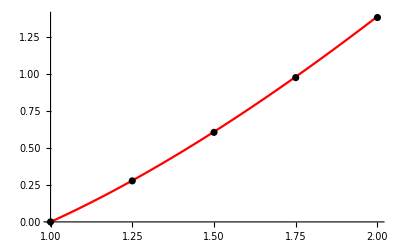

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+2/3 h,y+2/3 k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/4 k1 +3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 1. y_i = 0. k1 = 0.25 k2 = 0.277778 k3 = 0.280864 k4 = 0.306173 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.278909 k1 = 0.305782 k2 = 0.328509 k3 = 0.330575 k4 = 0.351581 y_точно = 0.278929 истинска грешка = 0.0000199741

i = 2 x_i = 1.5 y_i = 0.608165 k1 = 0.351361 k2 = 0.370592 k3 = 0.372071 k4 = 0.390034 y_точно = 0.608198 истинска грешка = 0.0000329341

i = 3 x_i = 1.75 y_i = 0.979285 k1 = 0.389898 k2 = 0.406564 k3 = 0.407676 k4 = 0.42337 y_точно = 0.979328 истинска грешка = 0.0000430257

i = 4 x_i = 2. y_i = 1.38624 k1 = 0.42328 k2 = 0.437986 k3 = 0.438851 k4 = 0.452788 y_точно = 1.38629 истинска грешка = 0.0000517723

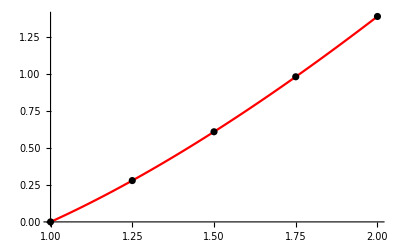

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+1/2 h,y+1/2 k1];
k3 =  h*f[x+1/2 h,y+1/2 k2];
k4 =  h*f[x+h,y+k3];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," k3 = ",k3," k4 = ",k4," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,1,2}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

## Задача подобна на а) от домашната

търсим точно частно решение:

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x]-5 Sin[x], y[3] == 7}, y[x],x]
```

{{y[x]→(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)}}

### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 3. y_i = 7. k1 = 1.5736 k2 = 2.27864 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.25 y_i = 8.92612 k1 = 2.36677 k2 = 3.2617 y_точно = 8.9573 истинска грешка = 0.0311786

i = 2 x_i = 3.5 y_i = 11.7404 k1 = 3.37357 k2 = 4.49293 y_точно = 11.8218 истинска грешка = 0.0814737

i = 3 x_i = 3.75 y_i = 15.6736 k1 = 4.63285 k2 = 6.02262 y_точно = 15.8314 истинска грешка = 0.157744

i = 4 x_i = 4. y_i = 21.0013 k1 = 6.19634 k2 = 7.91816 y_точно = 21.2705 истинска грешка = 0.269194

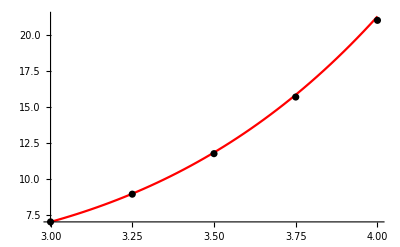

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+h,y+k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (1/2,1/2) - модифициран метод на Ойлер

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 3. y_i = 7. k1 = 1.5736 k2 = 1.92596 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.25 y_i = 8.92596 k1 = 2.36673 k2 = 2.81645 y_точно = 8.9573 истинска грешка = 0.0313404

i = 2 x_i = 3.5 y_i = 11.7424 k1 = 3.37408 k2 = 3.93836 y_точно = 11.8218 истинска грешка = 0.0794253

i = 3 x_i = 3.75 y_i = 15.6808 k1 = 4.63464 k2 = 5.33628 y_точно = 15.8314 истинска грешка = 0.150586

i = 4 x_i = 4. y_i = 21.017 k1 = 6.20027 k2 = 7.06978 y_точно = 21.2705 истинска грешка = 0.253495

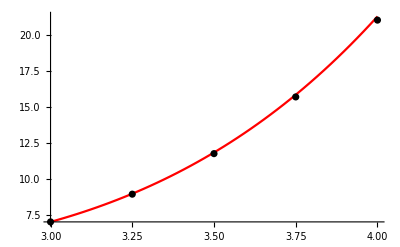

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+h/2,y+k1/2];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 3. y_i = 7. k1 = 1.5736 k2 = 2.04361 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.25 y_i = 8.9261 k1 = 2.36677 k2 = 2.96551 y_точно = 8.9573 истинска грешка = 0.0311961

i = 2 x_i = 3.5 y_i = 11.7419 k1 = 3.37396 k2 = 4.12441 y_точно = 11.8218 истинска грешка = 0.0799046

i = 3 x_i = 3.75 y_i = 15.6787 k1 = 4.63413 k2 = 5.56675 y_точно = 15.8314 истинска грешка = 0.152632

i = 4 x_i = 4. y_i = 21.0123 k1 = 6.19908 k2 = 7.3547 y_точно = 21.2705 истинска грешка = 0.258226

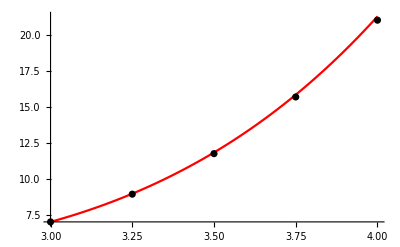

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+2/3 h,y+2/3 k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/4 k1 +3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 3. y_i = 7. k1 = 1.5736 k2 = 1.92596 k3 = 1.97001 k4 = 2.37775 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.25 y_i = 8.95721 k1 = 2.37455 k2 = 2.82524 k3 = 2.88158 k4 = 3.39818 y_точно = 8.9573 истинска грешка = 0.0000878897

i = 2 x_i = 3.5 y_i = 11.8216 k1 = 3.39388 k2 = 3.96063 k3 = 4.03148 k4 = 4.67772 y_точно = 11.8218 истинска грешка = 0.000229926

i = 3 x_i = 3.75 y_i = 15.8309 k1 = 4.67218 k2 = 5.37851 k3 = 5.4668 k4 = 6.27043 y_точно = 15.8314 истинска грешка = 0.000446637

i = 4 x_i = 4. y_i = 21.2698 k1 = 6.26345 k2 = 7.14086 k3 = 7.25054 k4 = 8.24882 y_точно = 21.2705 истинска грешка = 0.00076578

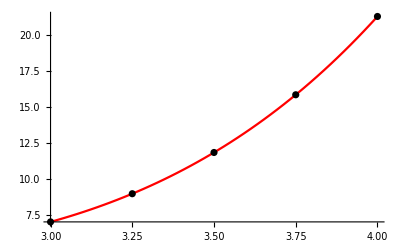

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+1/2 h,y+1/2 k1];
k3 =  h*f[x+1/2 h,y+1/2 k2];
k4 =  h*f[x+h,y+k3];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," k3 = ",k3," k4 = ",k4," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - при зададена стъпка h = 0.2

Мрежата е с n = 5. и стъпка h = 0.2

Теоретичната локална  грешка е 0.00032

Теоретичната глобална грешка е 0.0016

i = 0 x_i = 3. y_i = 7. k1 = 1.25888 k2 = 1.48431 k3 = 1.50685 k4 = 1.75974 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.2 y_i = 8.50016 k1 = 1.75841 k2 = 2.03362 k3 = 2.06114 k4 = 2.3678 y_точно = 8.50019 истинска грешка = 0.0000285119

i = 2 x_i = 3.4 y_i = 10.5528 k1 = 2.3661 k2 = 2.69795 k3 = 2.73113 k4 = 3.0993 y_точно = 10.5528 истинска грешка = 0.0000708182

i = 3 x_i = 3.6 y_i = 13.2734 k1 = 3.09719 k2 = 3.49423 k3 = 3.53393 k4 = 3.97332 y_точно = 13.2735 истинска грешка = 0.000130997

i = 4 x_i = 3.8 y_i = 16.7945 k1 = 3.97076 k2 = 4.44374 k3 = 4.49104 k4 = 5.01391 y_точно = 16.7947 истинска грешка = 0.000214233

i = 5 x_i = 4. y_i = 21.2702 k1 = 5.01085 k2 = 5.57341 k3 = 5.62966 k4 = 6.25155 y_точно = 21.2705 истинска грешка = 0.000327137

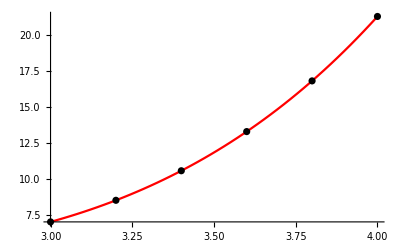

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
h = 0.2;
 n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+1/2 h,y+1/2 k1];
k3 =  h*f[x+1/2 h,y+1/2 k2];
k4 =  h*f[x+h,y+k3];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," k3 = ",k3," k4 = ",k4," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - при зададена стъпка h = 0.02

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална  грешка е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0 x_i = 3. y_i = 7. k1 = 0.125888 k2 = 0.128138 k3 = 0.12816 k4 = 0.130434 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.02 y_i = 7.12815 k1 = 0.130434 k2 = 0.132731 k3 = 0.132754 k4 = 0.135076 y_точно = 7.12815 истинска грешка = 2.75027×10^-10

i = 2 x_i = 3.04 y_i = 7.2609 k1 = 0.135076 k2 = 0.137422 k3 = 0.137446 k4 = 0.139817 y_точно = 7.2609 истинска грешка = 5.62528×10^-10

i = 3 x_i = 3.06 y_i = 7.39834 k1 = 0.139817 k2 = 0.142212 k3 = 0.142236 k4 = 0.144656 y_точно = 7.39834 истинска грешка = 8.62842×10^-10

i = 4 x_i = 3.08 y_i = 7.54057 k1 = 0.144656 k2 = 0.147101 k3 = 0.147125 k4 = 0.149596 y_точно = 7.54057 истинска грешка = 1.17632×10^-9

i = 5 x_i = 3.1 y_i = 7.68768 k1 = 0.149596 k2 = 0.152091 k3 = 0.152116 k4 = 0.154637 y_точно = 7.68768 истинска грешка = 1.50331×10^-9

i = 6 x_i = 3.12 y_i = 7.83979 k1 = 0.154637 k2 = 0.157183 k3 = 0.157208 k4 = 0.159781 y_точно = 7.83979 истинска грешка = 1.84417×10^-9

i = 7 x_i = 3.14 y_i = 7.99699 k1 = 0.159781 k2 = 0.162378 k3 = 0.162404 k4 = 0.165029 y_точно = 7.99699 истинска грешка = 2.19929×10^-9

i = 8 x_i = 3.16 y_i = 8.15939 k1 = 0.165028 k2 = 0.167678 k3 = 0.167705 k4 = 0.170382 y_точно = 8.15939 истинска грешка = 2.56904×10^-9

i = 9 x_i = 3.18 y_i = 8.32708 k1 = 0.170381 k2 = 0.173084 k3 = 0.173111 k4 = 0.175841 y_точно = 8.32708 истинска грешка = 2.95381×10^-9

i = 10 x_i = 3.2 y_i = 8.50019 k1 = 0.175841 k2 = 0.178598 k3 = 0.178625 k4 = 0.181409 y_точно = 8.50019 истинска грешка = 3.35401×10^-9

i = 11 x_i = 3.22 y_i = 8.6788 k1 = 0.181409 k2 = 0.184219 k3 = 0.184247 k4 = 0.187086 y_точно = 8.6788 истинска грешка = 3.77003×10^-9

i = 12 x_i = 3.24 y_i = 8.86304 k1 = 0.187086 k2 = 0.189951 k3 = 0.18998 k4 = 0.192873 y_точно = 8.86304 истинска грешка = 4.2023×10^-9

i = 13 x_i = 3.26 y_i = 9.05301 k1 = 0.192873 k2 = 0.195794 k3 = 0.195824 k4 = 0.198773 y_точно = 9.05301 истинска грешка = 4.65124×10^-9

i = 14 x_i = 3.28 y_i = 9.24882 k1 = 0.198773 k2 = 0.201751 k3 = 0.20178 k4 = 0.204787 y_точно = 9.24882 истинска грешка = 5.11731×10^-9

i = 15 x_i = 3.3 y_i = 9.45059 k1 = 0.204786 k2 = 0.207821 k3 = 0.207851 k4 = 0.210915 y_точно = 9.45059 истинска грешка = 5.60094×10^-9

i = 16 x_i = 3.32 y_i = 9.65843 k1 = 0.210915 k2 = 0.214007 k3 = 0.214038 k4 = 0.21716 y_точно = 9.65843 истинска грешка = 6.1026×10^-9

i = 17 x_i = 3.34 y_i = 9.87246 k1 = 0.21716 k2 = 0.220311 k3 = 0.220343 k4 = 0.223524 y_точно = 9.87246 истинска грешка = 6.62276×10^-9

i = 18 x_i = 3.36 y_i = 10.0928 k1 = 0.223523 k2 = 0.226734 k3 = 0.226766 k4 = 0.230007 y_точно = 10.0928 истинска грешка = 7.16191×10^-9

i = 19 x_i = 3.38 y_i = 10.3195 k1 = 0.230007 k2 = 0.233277 k3 = 0.23331 k4 = 0.236611 y_точно = 10.3195 истинска грешка = 7.72054×10^-9

i = 20 x_i = 3.4 y_i = 10.5528 k1 = 0.236611 k2 = 0.239943 k3 = 0.239976 k4 = 0.243339 y_точно = 10.5528 истинска грешка = 8.29915×10^-9

i = 21 x_i = 3.42 y_i = 10.7928 k1 = 0.243339 k2 = 0.246732 k3 = 0.246766 k4 = 0.250191 y_точно = 10.7928 истинска грешка = 8.89827×10^-9

i = 22 x_i = 3.44 y_i = 11.0396 k1 = 0.250191 k2 = 0.253647 k3 = 0.253682 k4 = 0.25717 y_точно = 11.0396 истинска грешка = 9.51844×10^-9

i = 23 x_i = 3.46 y_i = 11.2932 k1 = 0.25717 k2 = 0.26069 k3 = 0.260725 k4 = 0.264278 y_точно = 11.2932 истинска грешка = 1.01602×10^-8

i = 24 x_i = 3.48 y_i = 11.5539 k1 = 0.264278 k2 = 0.267862 k3 = 0.267898 k4 = 0.271515 y_точно = 11.5539 истинска грешка = 1.08241×10^-8

i = 25 x_i = 3.5 y_i = 11.8218 k1 = 0.271515 k2 = 0.275165 k3 = 0.275201 k4 = 0.278885 y_точно = 11.8218 истинска грешка = 1.15107×10^-8

i = 26 x_i = 3.52 y_i = 12.097 k1 = 0.278885 k2 = 0.282601 k3 = 0.282638 k4 = 0.286388 y_точно = 12.097 истинска грешка = 1.22206×10^-8

i = 27 x_i = 3.54 y_i = 12.3796 k1 = 0.286388 k2 = 0.290172 k3 = 0.290209 k4 = 0.294028 y_точно = 12.3796 истинска грешка = 1.29545×10^-8

i = 28 x_i = 3.56 y_i = 12.6698 k1 = 0.294027 k2 = 0.297879 k3 = 0.297918 k4 = 0.301805 y_точно = 12.6698 истинска грешка = 1.37128×10^-8

i = 29 x_i = 3.58 y_i = 12.9677 k1 = 0.301805 k2 = 0.305726 k3 = 0.305765 k4 = 0.309722 y_точно = 12.9677 истинска грешка = 1.44964×10^-8

i = 30 x_i = 3.6 y_i = 13.2735 k1 = 0.309722 k2 = 0.313714 k3 = 0.313754 k4 = 0.317782 y_точно = 13.2735 истинска грешка = 1.53057×10^-8

i = 31 x_i = 3.62 y_i = 13.5872 k1 = 0.317781 k2 = 0.321845 k3 = 0.321885 k4 = 0.325985 y_точно = 13.5872 истинска грешка = 1.61415×10^-8

i = 32 x_i = 3.64 y_i = 13.9091 k1 = 0.325985 k2 = 0.330121 k3 = 0.330162 k4 = 0.334335 y_точно = 13.9091 истинска грешка = 1.70044×10^-8

i = 33 x_i = 3.66 y_i = 14.2393 k1 = 0.334335 k2 = 0.338544 k3 = 0.338586 k4 = 0.342834 y_точно = 14.2393 истинска грешка = 1.78952×10^-8

i = 34 x_i = 3.68 y_i = 14.5778 k1 = 0.342834 k2 = 0.347118 k3 = 0.347161 k4 = 0.351483 y_точно = 14.5778 истинска грешка = 1.88146×10^-8

i = 35 x_i = 3.7 y_i = 14.925 k1 = 0.351483 k2 = 0.355843 k3 = 0.355887 k4 = 0.360286 y_точно = 14.925 истинска грешка = 1.97632×10^-8

i = 36 x_i = 3.72 y_i = 15.2808 k1 = 0.360286 k2 = 0.364724 k3 = 0.364768 k4 = 0.369245 y_точно = 15.2808 истинска грешка = 2.07419×10^-8

i = 37 x_i = 3.74 y_i = 15.6456 k1 = 0.369245 k2 = 0.373761 k3 = 0.373806 k4 = 0.378362 y_точно = 15.6456 истинска грешка = 2.17514×10^-8

i = 38 x_i = 3.76 y_i = 16.0194 k1 = 0.378362 k2 = 0.382957 k3 = 0.383003 k4 = 0.38764 y_точно = 16.0194 истинска грешка = 2.27925×10^-8

i = 39 x_i = 3.78 y_i = 16.4024 k1 = 0.387639 k2 = 0.392316 k3 = 0.392362 k4 = 0.397081 y_точно = 16.4024 истинска грешка = 2.3866×10^-8

i = 40 x_i = 3.8 y_i = 16.7947 k1 = 0.39708 k2 = 0.401839 k3 = 0.401887 k4 = 0.406688 y_точно = 16.7947 истинска грешка = 2.49727×10^-8

i = 41 x_i = 3.82 y_i = 17.1966 k1 = 0.406687 k2 = 0.41153 k3 = 0.411578 k4 = 0.416463 y_точно = 17.1966 истинска грешка = 2.61135×10^-8

i = 42 x_i = 3.84 y_i = 17.6082 k1 = 0.416463 k2 = 0.42139 k3 = 0.42144 k4 = 0.426411 y_точно = 17.6082 истинска грешка = 2.72892×10^-8

i = 43 x_i = 3.86 y_i = 18.0296 k1 = 0.42641 k2 = 0.431424 k3 = 0.431474 k4 = 0.436532 y_точно = 18.0296 истинска грешка = 2.85008×10^-8

i = 44 x_i = 3.88 y_i = 18.461 k1 = 0.436532 k2 = 0.441633 k3 = 0.441684 k4 = 0.446831 y_точно = 18.461 истинска грешка = 2.97491×10^-8

i = 45 x_i = 3.9 y_i = 18.9027 k1 = 0.446831 k2 = 0.452021 k3 = 0.452073 k4 = 0.45731 y_точно = 18.9027 истинска грешка = 3.10352×10^-8

i = 46 x_i = 3.92 y_i = 19.3548 k1 = 0.45731 k2 = 0.462591 k3 = 0.462644 k4 = 0.467973 y_точно = 19.3548 истинска грешка = 3.23598×10^-8

i = 47 x_i = 3.94 y_i = 19.8174 k1 = 0.467972 k2 = 0.473346 k3 = 0.4734 k4 = 0.478821 y_точно = 19.8174 истинска грешка = 3.37241×10^-8

i = 48 x_i = 3.96 y_i = 20.2908 k1 = 0.478821 k2 = 0.484289 k3 = 0.484344 k4 = 0.48986 y_точно = 20.2908 истинска грешка = 3.5129×10^-8

i = 49 x_i = 3.98 y_i = 20.7751 k1 = 0.48986 k2 = 0.495423 k3 = 0.495479 k4 = 0.501092 y_точно = 20.7751 истинска грешка = 3.65756×10^-8

i = 50 x_i = 4. y_i = 21.2705 k1 = 0.501091 k2 = 0.506752 k3 = 0.506808 k4 = 0.512519 y_точно = 21.2705 истинска грешка = 3.80648×10^-8

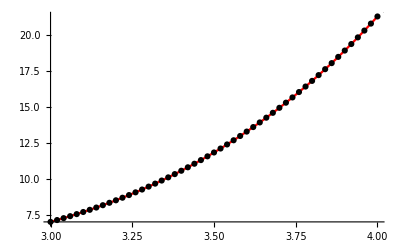

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
h = 0.02;
 n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+1/2 h,y+1/2 k1];
k3 =  h*f[x+1/2 h,y+1/2 k2];
k4 =  h*f[x+h,y+k3];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," k3 = ",k3," k4 = ",k4," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - при достигане на определена точност 10^-6

```mathematica
Clear[n]
Reduce[((b-a)/n)^4<= 10^-6,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-31.6228||n≥31.6228

Мрежата е с n = 32 и стъпка h = 0.03125

Теоретичната локална  грешка е 2.98023×10^-8

Теоретичната глобална грешка е 9.53674×10^-7

i = 0 x_i = 3. y_i = 7. k1 = 0.1967 k2 = 0.202193 k3 = 0.202279 k4 = 0.207865 y_точно = 7. истинска грешка = 0.

i = 1 x_i = 3.03125 y_i = 7.20225 k1 = 0.207864 k2 = 0.213541 k3 = 0.213629 k4 = 0.219401 y_точно = 7.20225 истинска грешка = 2.56714×10^-9

i = 2 x_i = 3.0625 y_i = 7.41585 k1 = 0.2194 k2 = 0.225263 k3 = 0.225355 k4 = 0.231315 y_точно = 7.41585 истинска грешка = 5.31695×10^-9

i = 3 x_i = 3.09375 y_i = 7.64118 k1 = 0.231314 k2 = 0.237368 k3 = 0.237463 k4 = 0.243615 y_точно = 7.64118 истинска грешка = 8.2572×10^-9

i = 4 x_i = 3.125 y_i = 7.87861 k1 = 0.243614 k2 = 0.249862 k3 = 0.249959 k4 = 0.256308 y_точно = 7.87861 истинска грешка = 1.1396×10^-8

i = 5 x_i = 3.15625 y_i = 8.12854 k1 = 0.256307 k2 = 0.262752 k3 = 0.262853 k4 = 0.269401 y_точно = 8.12854 истинска грешка = 1.47416×10^-8

i = 6 x_i = 3.1875 y_i = 8.39136 k1 = 0.2694 k2 = 0.276048 k3 = 0.276152 k4 = 0.282904 y_точно = 8.39136 истинска грешка = 1.83029×10^-8

i = 7 x_i = 3.21875 y_i = 8.66747 k1 = 0.282902 k2 = 0.289755 k3 = 0.289862 k4 = 0.296822 y_точно = 8.66747 истинска грешка = 2.20888×10^-8

i = 8 x_i = 3.25 y_i = 8.9573 k1 = 0.296821 k2 = 0.303884 k3 = 0.303994 k4 = 0.311166 y_точно = 8.9573 истинска грешка = 2.61087×10^-8

i = 9 x_i = 3.28125 y_i = 9.26126 k1 = 0.311165 k2 = 0.318442 k3 = 0.318555 k4 = 0.325944 y_точно = 9.26126 истинска грешка = 3.03722×10^-8

i = 10 x_i = 3.3125 y_i = 9.57977 k1 = 0.325942 k2 = 0.333438 k3 = 0.333555 k4 = 0.341164 y_точно = 9.57977 истинска грешка = 3.48896×10^-8

i = 11 x_i = 3.34375 y_i = 9.91329 k1 = 0.341163 k2 = 0.348881 k3 = 0.349002 k4 = 0.356836 y_точно = 9.91329 истинска грешка = 3.96712×10^-8

i = 12 x_i = 3.375 y_i = 10.2623 k1 = 0.356835 k2 = 0.364781 k3 = 0.364905 k4 = 0.37297 y_точно = 10.2623 истинска грешка = 4.4728×10^-8

i = 13 x_i = 3.40625 y_i = 10.6271 k1 = 0.372969 k2 = 0.381148 k3 = 0.381276 k4 = 0.389576 y_точно = 10.6271 истинска грешка = 5.00713×10^-8

i = 14 x_i = 3.4375 y_i = 11.0083 k1 = 0.389575 k2 = 0.397991 k3 = 0.398123 k4 = 0.406663 y_точно = 11.0083 истинска грешка = 5.57128×10^-8

i = 15 x_i = 3.46875 y_i = 11.4064 k1 = 0.406662 k2 = 0.415322 k3 = 0.415457 k4 = 0.424244 y_точно = 11.4064 истинска грешка = 6.16646×10^-8

i = 16 x_i = 3.5 y_i = 11.8218 k1 = 0.424242 k2 = 0.43315 k3 = 0.43329 k4 = 0.442328 y_точно = 11.8218 истинска грешка = 6.79394×10^-8

i = 17 x_i = 3.53125 y_i = 12.2551 k1 = 0.442326 k2 = 0.451488 k3 = 0.451632 k4 = 0.460927 y_точно = 12.2551 истинска грешка = 7.45505×10^-8

i = 18 x_i = 3.5625 y_i = 12.7067 k1 = 0.460925 k2 = 0.470347 k3 = 0.470495 k4 = 0.480053 y_точно = 12.7067 истинска грешка = 8.15114×10^-8

i = 19 x_i = 3.59375 y_i = 13.1771 k1 = 0.480051 k2 = 0.48974 k3 = 0.489891 k4 = 0.499718 y_точно = 13.1771 истинска грешка = 8.88363×10^-8

i = 20 x_i = 3.625 y_i = 13.6669 k1 = 0.499717 k2 = 0.509677 k3 = 0.509833 k4 = 0.519936 y_точно = 13.6669 истинска грешка = 9.65399×10^-8

i = 21 x_i = 3.65625 y_i = 14.1767 k1 = 0.519934 k2 = 0.530174 k3 = 0.530334 k4 = 0.540719 y_точно = 14.1767 истинска грешка = 1.04638×10^-7

i = 22 x_i = 3.6875 y_i = 14.707 k1 = 0.540718 k2 = 0.551243 k3 = 0.551407 k4 = 0.562082 y_точно = 14.707 истинска грешка = 1.13145×10^-7

i = 23 x_i = 3.71875 y_i = 15.2583 k1 = 0.56208 k2 = 0.572898 k3 = 0.573067 k4 = 0.584038 y_точно = 15.2583 истинска грешка = 1.22079×10^-7

i = 24 x_i = 3.75 y_i = 15.8314 k1 = 0.584036 k2 = 0.595154 k3 = 0.595328 k4 = 0.606603 y_точно = 15.8314 истинска грешка = 1.31457×10^-7

i = 25 x_i = 3.78125 y_i = 16.4266 k1 = 0.606601 k2 = 0.618026 k3 = 0.618205 k4 = 0.629791 y_точно = 16.4266 истинска грешка = 1.41297×10^-7

i = 26 x_i = 3.8125 y_i = 17.0448 k1 = 0.629789 k2 = 0.64153 k3 = 0.641713 k4 = 0.653619 y_точно = 17.0448 истинска грешка = 1.51616×10^-7

i = 27 x_i = 3.84375 y_i = 17.6864 k1 = 0.653617 k2 = 0.665681 k3 = 0.66587 k4 = 0.678103 y_точно = 17.6864 истинска грешка = 1.62435×10^-7

i = 28 x_i = 3.875 y_i = 18.3522 k1 = 0.678101 k2 = 0.690498 k3 = 0.690691 k4 = 0.703261 y_точно = 18.3522 истинска грешка = 1.73773×10^-7

i = 29 x_i = 3.90625 y_i = 19.0428 k1 = 0.703259 k2 = 0.715996 k3 = 0.716195 k4 = 0.72911 y_точно = 19.0428 истинска грешка = 1.85651×10^-7

i = 30 x_i = 3.9375 y_i = 19.759 k1 = 0.729108 k2 = 0.742195 k3 = 0.742399 k4 = 0.755669 y_точно = 19.759 истинска грешка = 1.9809×10^-7

i = 31 x_i = 3.96875 y_i = 20.5013 k1 = 0.755667 k2 = 0.769113 k3 = 0.769323 k4 = 0.782957 y_точно = 20.5013 истинска грешка = 2.11114×10^-7

i = 32 x_i = 4. y_i = 21.2705 k1 = 0.782955 k2 = 0.79677 k3 = 0.796986 k4 = 0.810994 y_точно = 21.2705 истинска грешка = 2.24745×10^-7

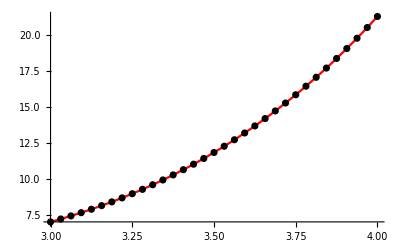

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 32;
h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 =  h*f[x+1/2 h,y+1/2 k1];
k3 =  h*f[x+1/2 h,y+1/2 k2];
k4 =  h*f[x+h,y+k3];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " k1 = ", k1, " k2 = ", k2," k3 = ",k3," k4 = ",k4," y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2k2+2k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - при достигане на определена точност 10^-13 - определяне мрежата без изчисления на резултатите

```mathematica
Clear[n]
Reduce[((b-a)/n)^4<= 10^-13,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-1778.28||n≥1778.28

```mathematica
(*въвеждаме условието на задачата*)
a = 3.; b = 4;
x = a;
y = 7.;
points = {{x,y}};
f[x_,y_]:= y-5 Sin[x]
(*точно решение*)
yt[x_]:=(14 ⅇ^x-5 ⅇ^x Cos[3]+5 ⅇ^3 Cos[x]-5 ⅇ^x Sin[3]+5 ⅇ^3 Sin[x])/(2 ⅇ^3)
(*съставяме мрежата*)
n = 1779;
h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 1779 и стъпка h = 0.000562114

Теоретичната локална  грешка е 5.61203×10^-17

Теоретичната глобална грешка е 9.98381×10^-14